```mathematica
spectralDensity:=Table[{i,(2*6.626*10^-34*i^3)/((3*10^8)^2)*1/((6.626*10^-34*i)/(1.3806*10^-23*5000)-1)},{i,-1000,1000}]
```

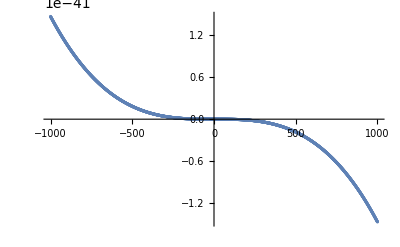

```mathematica
ListPlot@spectralDensity
```

```mathematica
spectralDensity:=Table[{i,(8*3.141592654*6.626*10^-34*(3*10^8)^2)/((3*10^8)^3)*i^3/((6.626*10^-34*i)/(1.3806*10^-23*5000)-1)},{i,0,1000}]
```

```mathematica
wavelengthRange:=Table[(3*i)/1000,{i,1,1000}]
spectralDensity:=Table[{wavelengthRange[[i]],(2*6.626*10^-34*(3*10^8)^2)/(wavelengthRange[[i]]^5*(3*10^8)^2)*1/((6.626*10^-34*3*10^8)/(wavelengthRange[[i]]^5 1.3806*10^-23*5000)-1)},{i,1,1000}]
```

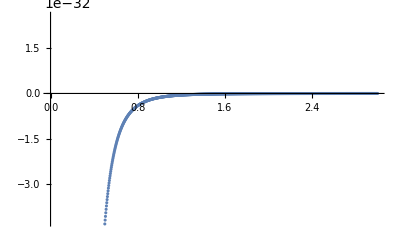

```mathematica
ListPlot@spectralDensity
```

```mathematica
spectralDensity:=Table[{i,i/((6.626*10^-27*i)/(1.3806*10^-16*1173.15)-1)},{i,-1000,1000}]
```

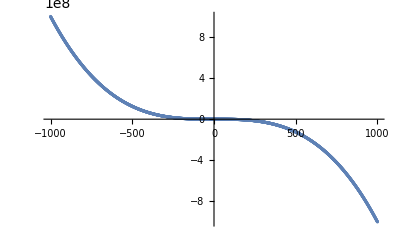

```mathematica
ListPlot@spectralDensity
```

```mathematica
spectralDensity:=Table[{i,(8*3.141592654*6.626*10^-27*(3*10^8)^2)/((3*10^8)^3)*i^3/((6.626*10^-27*i)/(1.3806*10^-16*5000)-1)},{i,0,1000}]
```

```mathematica
wavelengthRange:=Table[3*i*100000000,{i,1,1000}]
```

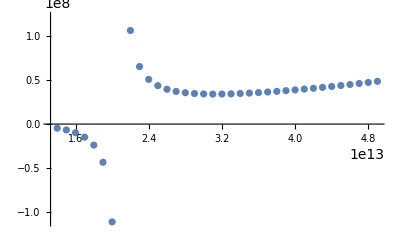

```mathematica
wavelengthRange:=Table[i*1000000000000,{i,0,1000}]
spectralDensity:=Table[{wavelengthRange[[i]],(8*3.141592654*6.626*10^-27*(3*10^8)^2)/((3*10^8)^3)*wavelengthRange[[i]]^3/((6.626*10^-27*wavelengthRange[[i]])/(1.3806*10^-16*1000)-1)},{i,15,50}]
ListPlot@spectralDensity
```

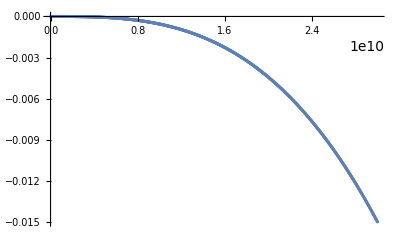

```mathematica
ListPlot@spectralDensity
```

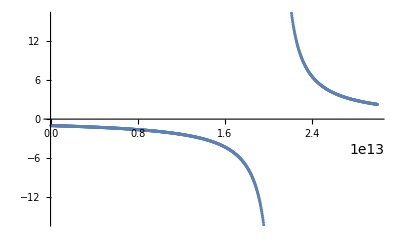

```mathematica
wavelengthRange:=Table[3*i*10000000000,{i,1,1000}]
spectralDensity:=Table[{wavelengthRange[[i]],1/((6.626*10^-27*wavelengthRange[[i]])/(1.3806*10^-16*1000)-1)},{i,1,1000}]
ListPlot@spectralDensity
```

```mathematica
wavelengthRange:=Range[2.3*10^13,2.6*10^13+1]
spectralDensity:=Table[{wavelengthRange[[i]],(8*3.141592654*6.626*10^-27*(3*10^8)^2)/((3*10^8)^3)*wavelengthRange[[i]]^3/((6.626*10^-27*wavelengthRange[[i]])/(1.3806*10^-16*1000)-1)},{i,1,Length@wavelengthRange}]
ListPlot@spectralDensity
```

General::nomem: The current computation was aborted because there was insufficient memory available to complete the computation.

Throw::sysexc: Uncaught SystemException returned to top level. Can be caught with Catch[…, _SystemException].

SystemException[MemoryAllocationFailure]

```mathematica
wavelengthRange:=Range[2.0*10^13,2.2*10^13+1000]
```

```mathematica
spectralDensity:=Table[{wavelengthRange[[i]],(8*3.141592654*6.626*10^-27*(3*10^8)^2)/((3*10^8)^3)*wavelengthRange[[i]]^3/((6.626*10^-27*wavelengthRange[[i]])/(1.3806*10^-16*1000)-1)},{i,1,Length@wavelengthRange}]
ListPlot@spectralDensity
```

General::nomem: The current computation was aborted because there was insufficient memory available to complete the computation.

Throw::sysexc: Uncaught SystemException returned to top level. Can be caught with Catch[…, _SystemException].

SystemException[MemoryAllocationFailure]

```mathematica
wavelengthRange
```

General::nomem: The current computation was aborted because there was insufficient memory available to complete the computation.

Throw::sysexc: Uncaught SystemException returned to top level. Can be caught with Catch[…, _SystemException].

SystemException[MemoryAllocationFailure]

```mathematica
1
```

```mathematica
wavelengthRange:=Range[2.3*10^13,2.6*10^13+1,.1]
```

```mathematica
wavelengthRange
```

General::nomem: The current computation was aborted because there was insufficient memory available to complete the computation.

Throw::sysexc: Uncaught SystemException returned to top level. Can be caught with Catch[…, _SystemException].

SystemException[MemoryAllocationFailure]

```mathematica
rightLength=30000
rightLength2=100000
waveLengthRange:=Table[2.42*10^13+i*2*10^14,{i,1,rightLength}]

waveLengthRange2:=Table[2.42*10^13+i*2*10^17,{i,rightLength+rightLength2,rightLength+2*rightLength2}]

AppendTo[waveLengthRange,waveLengthRange2];
lengthOfList:=Length@waveLengthRange
spectralDensity:=Table[{waveLengthRange[[i]],(8*3.141592654*6.626*10^-27*(3*10^8)^2)/((3*10^8)^3)*waveLengthRange[[i]]^3/((6.626*10^-27*waveLengthRange[[i]])/(1.3806*10^-16*1000)-1)},{i,1,lengthOfList}]

ListPlot@spectralDensity
```

30000

100000

-Graphics-

```mathematica
Manipulate
```

```mathematica
rightLength=1
rightLength2=1000
waveLengthRange2:=Table[2*10^17+i*2*10^14,{i,0,rightLength2*10}]
spectralDensity2:=Table[{waveLengthRange2[[i]],(8*3.141592654*6.626*10^-27*(3*10^8)^2)/((3*10^8)^3)*waveLengthRange2[[i]]^3/((6.626*10^-27*waveLengthRange2[[i]])/(1.3806*10^-16*1000)-1)},{i,1,Length@waveLengthRange2}]
ListPlot@spectralDensity2
```

1

1000

-Graphics-

1

1000

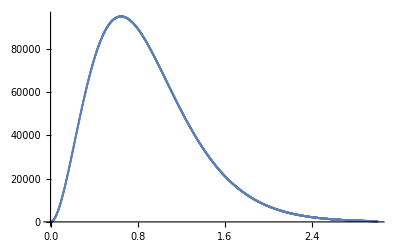

```mathematica
rightLength=1
rightLength2=1000
waveLengthRange2:=Table[1.08*10^10+i*1*10^11,{i,0,3000}]
spectralDensity2:=Table[{waveLengthRange2[[i]],(8*3.141592654*6.626*10^-27*(3*10^10)^2)/((3*10^10)^3)*waveLengthRange2[[i]]^3/(Exp[(6.626*10^-27*waveLengthRange2[[i]])/(1.3806*10^-16*1100)]-1)},{i,1,Length@waveLengthRange2}]
ListPlot@spectralDensity2
```

```mathematica
10
```

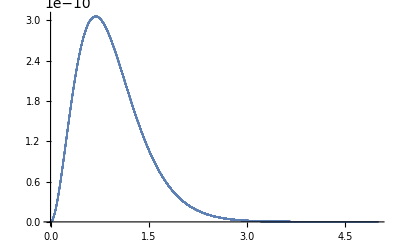

```mathematica
wavelengthRange:=Table[(3*i)/1000,{i,1,1000}]
spectralDensity:=Table[{i,(2*6.626*10^-34*i^3)/((3*10^8)^2)*1/(Exp[(6.626*10^-34*i)/(1.3806*10^-23*1173)]-1)},{i,1,500000000000000,10000000000}]
ListPlot@spectralDensity
```

General::munfl: 1.19268×10^24 1.35725541566×10^-417 is too small to represent as a normalized machine number; precision may be lost.

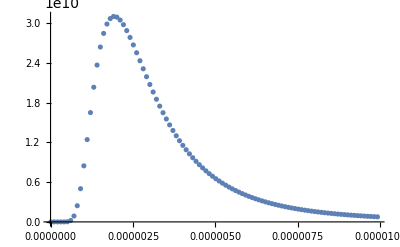

```mathematica
spectralDensity:=Table[{i,(2*6.626*10^-34*(3*10^8)^2)/i^5*1/(Exp[(6.626*10^-34*3*10^8)/(i*1.3806*10^-23*1500)]-1)},{i,.00000001,.00001,1/10000000}]
ListPlot@spectralDensity
```

```mathematica
https://physics.stackexchange.com/questions/648273/does-fire-emit-black-body-radiation
```